```mathematica
S[q_] := Block[{G1,G2, fi},
fi = FactorInteger[q];
G1 = q Times @@ ((1 -1/#[[1]])^#[[2]] &  /@fi);
G2=q^2 Times @@ ((1 -1/#[[1]]^2)^#[[2]] &  /@fi);
- G1 + 1/3G2
];
```

```mathematica
Select[Table[{q,S[q]},{q,2,1000}],Negative[#[[2]]]&]
```

{}

```mathematica
ClearAll[MB];
```

```mathematica
MB[M_] := 
MB[M] =
Sum[N[S[q],20],{q,2,M}]/Sum[N[EulerPhi[q],20],{q,2,M}]
```

```mathematica
MB[500000]
```

136416.8932829190255

```mathematica
MBT=ParallelTable[{M,Pi^2MB[M]},{M,500000,500100}];
```

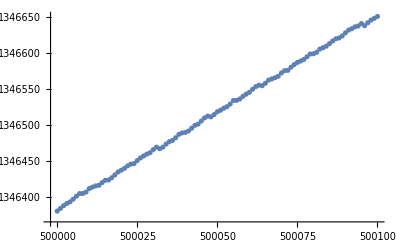

```mathematica
ListPlot[MBT]
```

```mathematica
logmodel = LinearModelFit[Log[MBT],{x},x]
```

FittedModel[«59»+«59» x]

```mathematica
Normal[logmodel]
```

0.95382637306447160562+1.0028000056908098474 x

```mathematica
N[logmodel["ParameterTable"],6]
```

| Estimate | Standard Error | t-Statistic | P-Value
1. | 0.953826 | 0.0247808 | 38.4906 | 2.29105×10^-61
x | 1.0028 | 0.00188842 | 531.025 | 7.81806×10^-173

```mathematica
linmodel = LinearModelFit[MBT,{x},x]
```

FittedModel[-«62»+«59» x]

```mathematica
Normal[linmodel]
```

-3770.001303883831885+2.70030639870413978 x

```mathematica
nonlinmodel = NonlinearModelFit[Log[MBT],{a + x},a,x]
```

FittedModel[«59»+x]

```mathematica
Normal[nonlinmodel]
```

0.99056934517988938398+x

```mathematica
N[Exp[nonlinmodel[Log[M]]],4]
```

2.693 M

```mathematica
ShowFitLogModel[data_, model_, title_]:=
Show[
ListPlot[data, PlotStyle->{Red, PointSize[0.01]},PlotLegends->{"data"}],
Plot[Exp[model[Log[x]]],{x,data[[1,1]],data[[-1,1]]},PlotStyle->{Green, Thick},
PlotLegends->{N[Exp[model[Log[N]]],5]},PlotRange->All],
PlotLabel->title,
AxesLabel->{"N", "<S(q)>"}
];
```

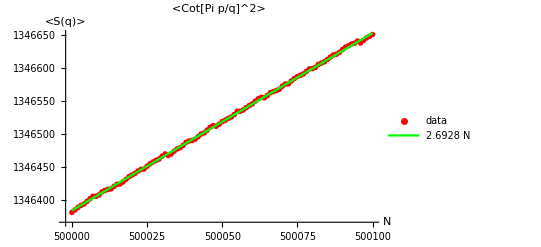

```mathematica
ShowFitLogModel[MBT, nonlinmodel, "<Cot[Pi p/q]^2>"]
```

```mathematica
N[nonlinmodel["ParameterTable"],6]
```

| Estimate | Standard Error | t-Statistic | P-Value
a | 0.990569 | 1.1076×10^-7 | 8.9434×10^6 | 5.631×10^-597